# FindRandomGridMazeSolution

Find a solution to a random grid maze

## Definition

```mathematica
PositiveIntegerQ//ClearAll
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
PositiveIntegerQ::usage="PositiveIntegerQ[n] returns True when n is a strictly positive integer.";
```

```mathematica
ClearAll[FindRandomGridMazeSolution]
```

```mathematica
FindRandomGridMazeSolution::usage="FindRandomGridMazeSolution[{m,n}] finds a solution and other data for a random grid maze of size m by n.";
```

```mathematica
FindRandomGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges. This is known as the trivial graph, the singleton, or the unit graph.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=GridGraph[{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->Iconize[shortestPath,"shortest-path"],"distance"->GraphDistance[m,start,end],"shortest-path-subgraph"->shortestPathSubgraph|>](*some ideas for other properties to add include deadends.*)
```

## Documentation

### Usage

FindRandomGridMazeSolution[{m,n}]

finds a solution to a random maze of size m by n.

### Details & Options

How does this compare with https://resources.wolframcloud.com/FunctionRepository/resources/RandomMaze/ using the option "ShowSolution"-> True? 
Can you make an example comparing the two functions?
If the functionalities mainly overlap, we may reject this submission in favor of the existing resource function, unless you can show significant advantages in performance or functionality for your function.

The keys following the convention of alphanumeric characters lowercase separated by dash and hyphen, which is the convention for URLs and GitHub Repositories and which the ResourceFunction SlugifyString converts strings to.

This is from the documentation for FindShortestPath under Applications, third example where it states “Create a maze by random depth-first search of a grid graph:". I guess this functions depth-first search algorithm is faster than RandomMazes' breadth-first search algorithm. I didn't write the code for this function and I don't fully understand it, so I will give credit to the developers who built FindShortestPath.

I realize that some of my comments are specific to justifying this function and I don't want to be attacking or criticizing RandomMaze by making a straw man argument and comparing bad good to good code, but I put them to get the ResourceFunction published.

## Examples

### Basic Examples

Find a solution to a random 5 by 5 maze:

```mathematica
FindRandomGridMazeSolution[{5,5}]
```

-Graphics-

Find a solution to a random 10 by 10 maze:

```mathematica
FindRandomGridMazeSolution[{10,10}]
```

-Graphics-

Find a solution to a random 15 by 15 maze:

```mathematica
FindRandomGridMazeSolution[{15,15}]
```

-Graphics-

### Scope

FindRandomGridMaze solution supports rectangular graphs where the height and width are different:

RandomMaze only supports square mazes.

A long short rectangular maze:

```mathematica
FindRandomGridMazeSolution[{21,54}]
```

-Graphics-

A tall skinny narrow rectangular maze:

```mathematica
FindRandomGridMazeSolution[{54,21}]
```

-Graphics-

The function supports small mazes. Make a random 7 by 7 maze:

```mathematica
FindRandomGridMazeSolution[{7,7}]
```

-Graphics-

Make a random 10 by 10 maze:

```mathematica
FindRandomGridMazeSolution[{10,10}]
```

-Graphics-

The function supports big mazes, too. Make a random 20 by 20 maze:

```mathematica
FindRandomGridMazeSolution[{20,20}]
```

-Graphics-

Make a random 25 by 25 maze:

```mathematica
FindRandomGridMazeSolution[{25,25}]
```

-Graphics-

Make a random 30 by 30 maze:

```mathematica
FindRandomGridMazeSolution[{30,30}]
```

-Graphics-

Make a random 35 by 35 maze:

```mathematica
FindRandomGridMazeSolution[{35,35}]
```

-Graphics-

Make a random 40 by 40 maze and compute the timing:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{40,40}]]
```

0.1713

-Graphics-

Make a random 45 by 45 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{45,45}]]
```

0.232111

-Graphics-

Make a random 50 by 50 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{50,50}]]
```

0.299831

-Graphics-

Make a random 55 by 55 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{55,55}]]
```

0.433257

-Graphics-

Make a random 60 by 60 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{60,60}]]
```

0.539138

-Graphics-

Make a random 65 by 65 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{65,65}]]
```

0.70903

-Graphics-

Make a random 70 by 70 maze. At this point, the maze and solved maze start getting hard to see, so the shortest-path subgraph is advantageous because its easier to see.:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{70,70}]]
```

0.841246

-Graphics-

Make a random 75 by 75 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{75,75}]]
```

1.10421

-Graphics-

Make a random 80 by 80 maze (at this point even the shortest-path subgraph is getting hard to understand):

```mathematica
EchoTiming[FindRandomGridMazeSolution[{80,80}]]
```

1.37651

-Graphics-

Make a random 85 by 85 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{85,85}]]
```

1.64872

-Graphics-

We are approaching the limit of this function. We cannot go past 100 by 100 without using GraphPlot:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{90,90}]]
```

1.96134

-Graphics-

Make a random 95 by 95 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{95,95}]]
```

2.40227

-Graphics-

Make a random 100 by 100 maze:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{100,100}]]
```

2.96479

-Graphics-

Make a plot of a 101 by 101 maze. Unfortunately, GraphPlot is required for graphs with more than 10,000 edges, I think, which returns a Graphics object instead of a Graph object.

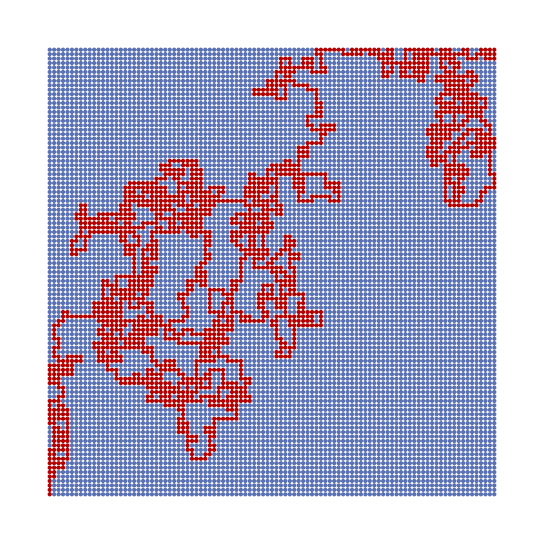

```mathematica
GraphPlot[FindRandomGridMazeSolution[{101,101}]["solved-maze"]]
```

105 by 105:

```mathematica
EchoTiming[GraphPlot[FindRandomGridMazeSolution[{105,105}]["solved-maze"]]]
```

9.80543

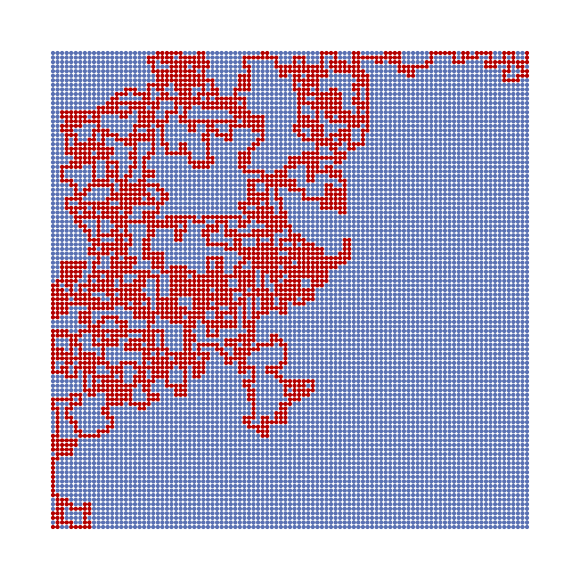

110 by 110:

```mathematica
EchoTiming[GraphPlot[FindRandomGridMazeSolution[{110,110}]["solved-maze"]]]
```

11.4477

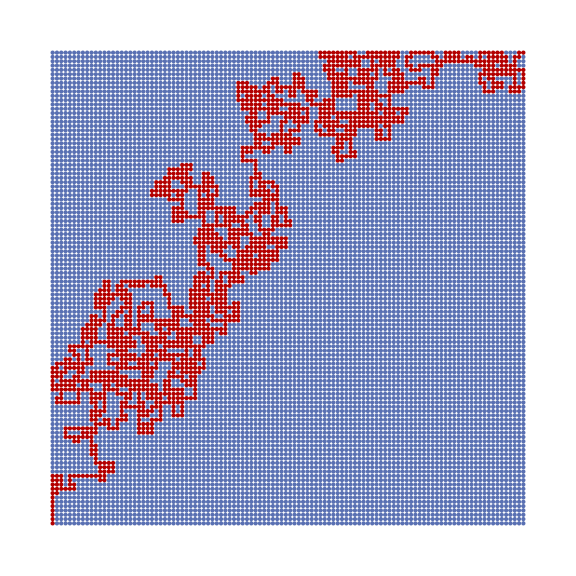

Ceiling of exp(5) is 149:

```mathematica
Table[n->Ceiling[Exp[n]],{n,20}]
```

{1→3,2→8,3→21,4→55,5→149,6→404,7→1097,8→2981,9→8104,10→22027,11→59875,12→162755,13→442414,14→1202605,15→3269018,16→8886111,17→24154953,18→65659970,19→178482301,20→485165196}

A 149 by 149 maze (149 because ceiling of exp(5) is 149):

```mathematica
EchoTiming[GraphPlot[FindRandomGridMazeSolution[{149,149}]["solved-maze"]]]
```

34.7757

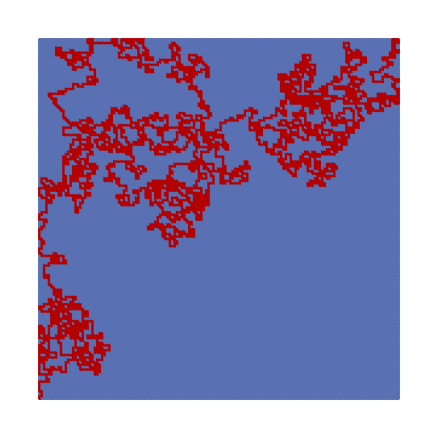

```mathematica
EchoTiming[GraphPlot[{{"[◼]", "FindRandomGridMazeSolution"}}[{101,101}]["solved-maze"]]]
```

10.4497

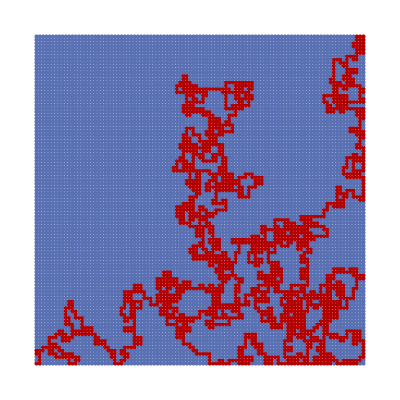

```mathematica
GraphQ[]
```

False

If we go up even by 1 to 101 by 101 the maze and solved-maze don't work.:

```mathematica
EchoTiming[FindRandomGridMazeSolution[{101,101}]]
```

2.98184

-Graphics-

The function returns a Graph, which can be used for further analysis.

### Properties & Relations

Compare the timing of FindRandomGridMazeSolution to RandomMaze:

```mathematica
EchoTiming@FindRandomGridMazeSolution[{100,100}]
```

2.93385

-Graphics-

```mathematica
First@RepeatedTiming@FindRandomGridMazeSolution[{100,100}]
```

2.94379

```mathematica
EchoTiming@ResourceFunction["RandomMaze"][100]
```

56.6464

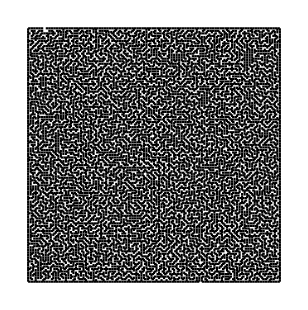

The function is about 19 times faster compared to RandomMaze:

```mathematica
56.6463813/2.9338526
```

19.3078

This function is much faster than RandomMaze for large inputs.

Here are some more timing tests. My approach will be to create a CloudExpression with CreateCloudExpression with an empty association <||> that I will put RepeatedTiming for mazes from 30 to 100 in increments of 10 for the ResourceFunction RandomMaze and my submission of FindRandomGridMazeSolution. I will then compare the total time it takes:

Create a cloud expression to store timing data for RandomMaze:

```mathematica
randomMazeTiming=CreateCloudExpression[<||>,"randomMazeTimingData"]
```

CloudExpression[…]

Store a value:

```mathematica
randomMazeTiming["30"]=First[Quiet[RepeatedTiming[ResourceFunction["RandomMaze"][30]],{First::nofirst,Part::take}]]
```

0.63955

Create a function to do iterate through the process of performing timing:

```mathematica
storeRandomMazeTimingFunction[x_?IntegerQ]:=randomMazeTiming[ToString[x]]=First[Quiet[RepeatedTiming[ResourceFunction["RandomMaze"][x]],{First::nofirst,Part::take}]]
```

Do the timing:

```mathematica
Do[storeRandomMazeTimingFunction[i],{i,30,100,10}]
```

Get the timing results:

```mathematica
Sort@Get[randomMazeTiming]
```

<|40→1.03409,30→2.18132,60→3.67364,50→13.8107,70→18.6532,80→40.6946,90→48.7303,100→197.233|>

This is a cloud expression for FindRandomGridMazeSolution:

```mathematica
FindRandomGridMazeSolutionTiming=CreateCloudExpression[<||>,"FindRandomGridMazeSolutionTiming"]
```

CloudExpression[…]

This is a function to time how fast FindRandomGridMazeSolution is:

```mathematica
findRandomGridMazeSolutionTimingFunction[x_?IntegerQ]:=FindRandomGridMazeSolutionTiming[ToString[x]]=First[Quiet[RepeatedTiming[FindRandomGridMazeSolution[x]],{First::nofirst,Part::take}]]
```

Do the timing:

```mathematica
Do[findRandomGridMazeSolutionTimingFunction[i],{i,30,100,10}]
```

Get the timing results:

```mathematica
Get[FindRandomGridMazeSolutionTiming]
```

<|30→2.10024×10^-8,40→2.23814×10^-8,50→2.08957×10^-8,60→2.21422×10^-8,70→2.09859×10^-8,80→2.19656×10^-8,90→2.20077×10^-8,100→2.16435×10^-8|>

Put the timing results in a dataset:

```mathematica
data=Dataset[<|"RandomMaze"->Get@randomMazeTiming,"FindRandomGridMazeSolution"->Get@FindRandomGridMazeSolutionTiming|>]
```

-Graphics-

Get totals for each row by applying Total to all columns for all the rows, then sort:

```mathematica
data[Sort,Total]
```

-Graphics-

Sort, then use the ResourceFunction ReadableTimeString to convert raw seconds into a human-readable amount of time:

```mathematica
data[Sort,ResourceFunction["ReadableTimeString"][#,"PrefixShort"->False,"Decimals"->3]&@*Total]
```

-Graphics-

Make a pie-chart (notice that FindRandomGridMazeSolution's times are consistent whereas RandomMaze keeps increasing in time):

```mathematica
data[All,PieChart]
```

-Graphics-

Make a bar-chart:

```mathematica
data[All,BarChart[#,]&]
```

-Graphics-

You can analyze the output of this function because its a graph:

I compare this function to RandomMaze.

```mathematica
data=FindRandomGridMazeSolution[{30,30}];
```

```mathematica
{ℱ,𝒢}={data["maze"],data["solved-maze"]}
```

{-Graphics-,-Graphics-}

Notice the purple border when you click the maze:

-Graphics-

You can’t analyze RandomMaze because its head is Graphics:

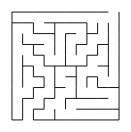

```mathematica
ResourceFunction["RandomMaze"][10]
```

Notice the orange border, indicating Graphics:

-Graphics-

```mathematica
Head[ResourceFunction["RandomMaze"][10]]
```

Graphics

To analyze a maze encoded in Graphics you would have to use image processing, such as MorphologicalGraph. For an example of this see Jon McLoone’s blog post:

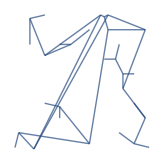

```mathematica
MorphologicalGraph[ResourceFunction["RandomMaze"][10]]
```

This is similar from a documentation example for MorphologicalGraph:

Conversion of a maze into a graph:

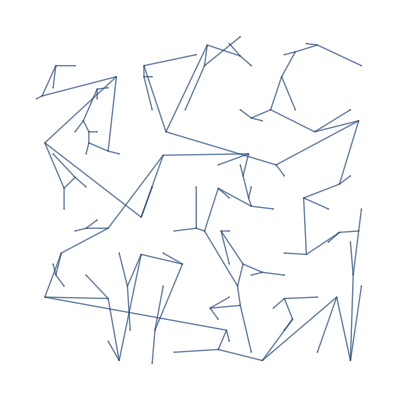

```mathematica
MorphologicalGraph[-Graphics-]
```

Here are some things you can analyze in the output maze, some more useful than others:

Adjacency matrix:

```mathematica
AdjacencyMatrix[𝒢]
```

SparseArray[…]

Color vertices:

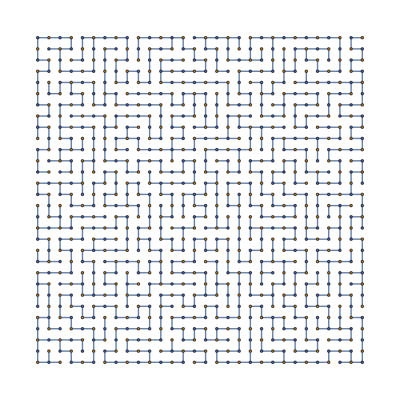

```mathematica
ResourceFunction["ColorGraphVertices"][ℱ]
```

Color edges:

```mathematica
ResourceFunction["ColorGraphEdges"][ℱ]
```

-Graphics-

Vertex chromatic number:

```mathematica
VertexChromaticNumber[ℱ]
```

2

Edge chromatic number:

```mathematica
EdgeChromaticNumber[ℱ]
```

4

The interesting thing is the chromatic polynomial matches the form (x-1)^(vertex count-1)x:

```mathematica
FullSimplify[ChromaticPolynomial[data["maze"],x]]//TraditionalForm
```

(x-1)^899 x

Vertex count:

```mathematica
VertexCount[ℱ]
```

900

Edge count:

```mathematica
EdgeCount[ℱ]
```

899

Vertex-degree:

```mathematica
NumericArray[VertexDegree[ℱ],"Integer8"]
```

NumericArray[…]

Highlight graph hubs, which have the greatest vertex degrees in the graph:

```mathematica
GraphHub[ℱ]
```

{380}

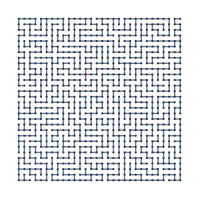

```mathematica
HighlightGraph[ℱ,GraphHub[ℱ]]
```

Highlight the start and end vertices:

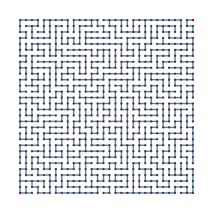

```mathematica
HighlightGraph[ℱ,{1,Last[VertexList[ℱ]]}]
```

Find the distance from the start to the end:

```mathematica
GraphDistance[ℱ,data["start"],data["end"]]
```

220

The data is already available:

```mathematica
data["distance"]
```

220

The mean graph distance:

```mathematica
MeanGraphDistance[data["maze"]]
```

2432206/13485

The distance matrix:

```mathematica
GraphDistanceMatrix[data["maze"]]
```

VertexEccentricity gives the length of the longest shortest path from the source s to every other vertex in the graph g:

```mathematica
VertexEccentricity[data["maze"],1]
```

340

```mathematica
VertexEccentricity[data["maze"],900]
```

416

GraphRadius gives the minimum eccentricity of the vertices in the graph g:

```mathematica
GraphRadius[data["maze"]]
```

268

Find the graph center, vertices with minimum eccentricity:

{462}

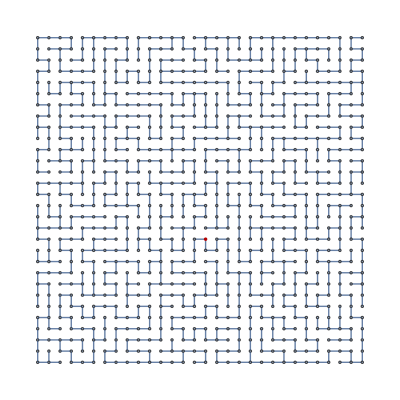

```mathematica
HighlightGraph[data["maze"],Echo@GraphCenter[data["maze"]]]
```

Notice that the graph center is on the solution path:

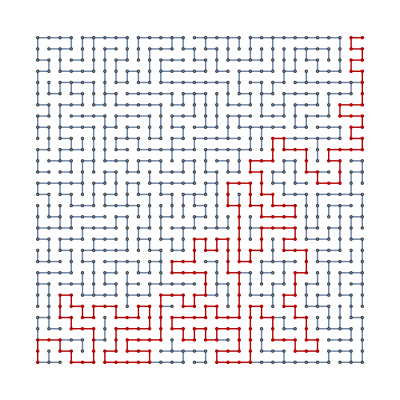

```mathematica
data["solved-maze"]
```

```mathematica
data["shortest-path"]
```

-Graphics-

```mathematica
SubsetQ[First@data["shortest-path"],GraphCenter[data["maze"]]]
```

True

GraphDiameter gives the greatest distance between any pair of vertices in the graph g:

```mathematica
GraphDiameter[data["maze"]]
```

536

GraphPeriphery gives vertices with maximum eccentricity:

{48,265,505}

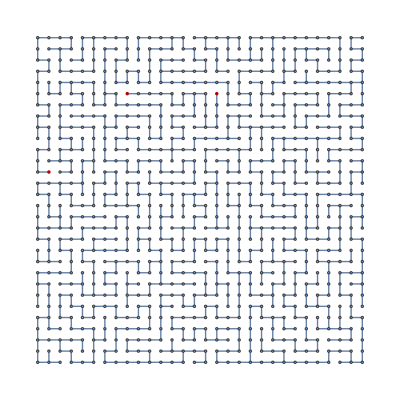

```mathematica
HighlightGraph[data["maze"],Echo@GraphPeriphery[data["maze"]]]
```

It seems like these are the farthest dead ends.

Find the number of vertices you need to delete to disconnect the graph:

```mathematica
VertexConnectivity[data["maze"]]
```

1

The edge connectivity of a graph g is the smallest number of edges whose deletion from g disconnects g:

```mathematica
EdgeConnectivity[data["maze"]]
```

1

GraphDensitypaclet:ref/GraphDensity is the ratio of the number of edges divided by the number of edges of a complete graph with the same number of vertices:

```mathematica
GraphDensity[data["maze"]]
```

1/450

Find how tightly connected a graph is compared to number of edges:

```mathematica
GraphLinkEfficiency[data["maze"]]
```

9690809/12123015

```mathematica
ResourceFunction["ReadableForm"][N[GraphLinkEfficiency[data["maze"]]]]
```

0.7993728457813506

ClosenessCentralitypaclet:ref/ClosenessCentrality will give high centralities to vertices that are at a short average distance to every other reachable vertex:

```mathematica
Short@ClosenessCentrality[data["maze"]]
```

{0.00694359,0.00699176,0.00704049,«894»,0.00551311,0.00548311,0.00539467}

BetweennessCentralitypaclet:ref/BetweennessCentrality will give high centralities to vertices that are on many shortest paths of other vertex pairs:

```mathematica
Short@BetweennessCentrality[data["maze"]]
```

{2688.,3580.,189150.,186048.,185794.,0.,898.,184586.,183144.,«883»,135228.,132618.,132090.,132968.,6244.,3580.,2688.,0.}

Get a ShortestPathFunction for fast computation:

```mathematica
f=FindShortestPath[data["maze"],All,All]
```

-Graphics-

You could also do work with cycles and tours.

FindPostmanTourpaclet:ref/FindPostmanTour[g] 
finds a Chinese postman tour in the graph g of minimal length.

Find a tour that traverses every edge at least once:

```mathematica
Short@FindPostmanTour[data["maze"]]
```

{{1<->31,31<->61,61<->31,31<->32,32<->31,31<->1,1<->2,2<->3,3<->33,33<->63,63<->93,93<->123,«1774»,38<->37,37<->36,36<->35,35<->34,34<->64,64<->34,34<->35,35<->5,5<->4,4<->3,3<->2,2<->1}}

The maze is acyclic:

```mathematica
AcyclicGraphQ[data["maze"]]
```

True

There is only one set of edges that leads to the end:

```mathematica
FindEdgeIndependentPaths[data["maze"],data["start"],data["end"],Infinity]
```

{{1,2,3,33,63,62,92,91,121,151,152,153,154,124,94,95,65,66,67,97,96,126,125,155,156,186,216,215,245,275,276,306,305,304,274,244,214,213,212,182,181,211,241,271,301,302,272,242,243,273,303,333,334,335,336,337,367,397,396,426,427,457,458,459,429,399,369,370,400,430,431,432,462,461,491,492,522,521,520,519,549,548,547,546,545,515,485,486,456,455,425,395,365,364,394,393,423,424,454,453,483,484,514,544,543,542,512,482,481,511,541,571,572,573,574,575,576,606,605,635,634,633,663,693,692,722,752,753,723,724,725,695,696,666,667,697,698,699,729,730,731,701,671,672,702,703,673,643,613,612,611,581,580,550,551,552,553,554,555,525,526,527,557,587,586,585,615,614,644,674,704,705,675,645,646,616,617,618,588,589,619,649,650,651,681,680,710,740,739,738,768,767,797,827,828,829,799,800,830,860,890,891,861,862,892,893,863,833,834,864,894,895,896,897,867,868,898,899,869,870,900}}

```mathematica
Length[FindEdgeIndependentPaths[data["maze"],data["start"],data["end"],Infinity]]===1
```

True

There is only one set of vertices that leads to the end:

```mathematica
FindVertexIndependentPaths[data["maze"],data["start"],data["end"],Infinity]
```

{{1,2,3,33,63,62,92,91,121,151,152,153,154,124,94,95,65,66,67,97,96,126,125,155,156,186,216,215,245,275,276,306,305,304,274,244,214,213,212,182,181,211,241,271,301,302,272,242,243,273,303,333,334,335,336,337,367,397,396,426,427,457,458,459,429,399,369,370,400,430,431,432,462,461,491,492,522,521,520,519,549,548,547,546,545,515,485,486,456,455,425,395,365,364,394,393,423,424,454,453,483,484,514,544,543,542,512,482,481,511,541,571,572,573,574,575,576,606,605,635,634,633,663,693,692,722,752,753,723,724,725,695,696,666,667,697,698,699,729,730,731,701,671,672,702,703,673,643,613,612,611,581,580,550,551,552,553,554,555,525,526,527,557,587,586,585,615,614,644,674,704,705,675,645,646,616,617,618,588,589,619,649,650,651,681,680,710,740,739,738,768,767,797,827,828,829,799,800,830,860,890,891,861,862,892,893,863,833,834,864,894,895,896,897,867,868,898,899,869,870,900}}

```mathematica
Length[FindVertexIndependentPaths[data["maze"],data["start"],data["end"],Infinity]]===1
```

True

The shortest path graph is a subgraph:

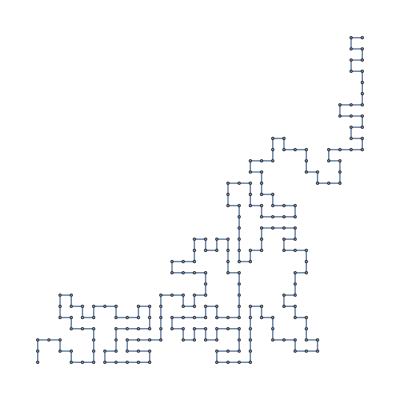

True

```mathematica
IsomorphicSubgraphQ[Echo@data["shortest-path-subgraph"],data["maze"]]
```

Find a subgraph isomorphism:

```mathematica
FindSubgraphIsomorphism[data["shortest-path-subgraph"],data["maze"]]
```

{<|1→1,2→2,3→3,33→33,63→63,62→62,92→92,91→91,121→121,151→151,152→152,153→153,154→154,124→124,94→94,95→95,65→65,66→66,67→67,97→97,96→96,126→126,125→125,155→155,156→156,186→186,216→216,215→215,245→245,275→275,276→276,306→306,305→305,304→304,274→274,244→244,214→214,213→213,212→212,182→182,181→181,211→211,241→241,271→271,301→301,302→302,272→272,242→242,243→243,273→273,303→303,333→333,334→334,335→335,336→336,337→337,367→367,397→397,396→396,426→426,427→427,457→457,458→458,459→459,429→429,399→399,369→369,370→370,400→400,430→430,431→431,432→432,462→462,461→461,491→491,492→492,522→522,521→521,520→520,519→519,549→549,548→548,547→547,546→546,545→545,515→515,485→485,486→486,456→456,455→455,425→425,395→395,365→365,364→364,394→394,393→393,423→423,424→424,454→454,453→453,483→483,484→484,514→514,544→544,543→543,542→542,512→512,482→482,481→481,511→511,541→541,571→571,572→572,573→573,574→574,575→575,576→576,606→606,605→605,635→635,634→634,633→633,663→663,693→693,692→692,722→722,752→752,753→753,723→723,724→724,725→725,695→695,696→696,666→666,667→667,697→697,698→698,699→699,729→729,730→730,731→731,701→701,671→671,672→672,702→702,703→703,673→673,643→643,613→613,612→612,611→611,581→581,580→580,550→550,551→551,552→552,553→553,554→554,555→555,525→525,526→526,527→527,557→557,587→587,586→586,585→585,615→615,614→614,644→644,674→674,704→704,705→705,675→675,645→645,646→646,616→616,617→617,618→618,588→588,589→589,619→619,649→649,650→650,651→651,681→681,680→680,710→710,740→740,739→739,738→738,768→768,767→767,797→797,827→827,828→828,829→829,799→799,800→800,830→830,860→860,890→890,891→891,861→861,862→862,892→892,893→893,863→863,833→833,834→834,864→864,894→894,895→895,896→896,897→866,867→865,868→835,898→805,899→804,869→803,870→773,900→743|>}

Find isomorphic subgraphs:

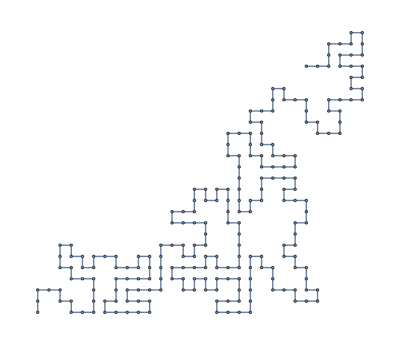

```mathematica
FindIsomorphicSubgraph[data["maze"],data["shortest-path-subgraph"]]
```

I will grant that RandomMaze does have nice Graphics. I might add an option for this. I tried looking at the source code for RandomMaze, but I couldn’t figure out a simple way to make Graphics.

Another advantage of this function compared to RandomGraph is you can generate rectangles and not just squares:

```mathematica
FindRandomGridMazeSolution[{50,40}]
```

-Graphics-

You can't do this with RandomMaze. You can do a 40 maze or a 50 maze but not both:

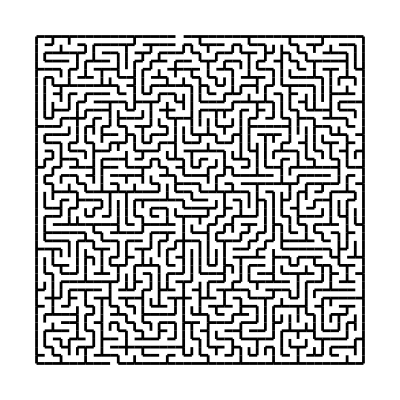

```mathematica
TimeConstrained[ResourceFunction["RandomMaze"][40],20]
```

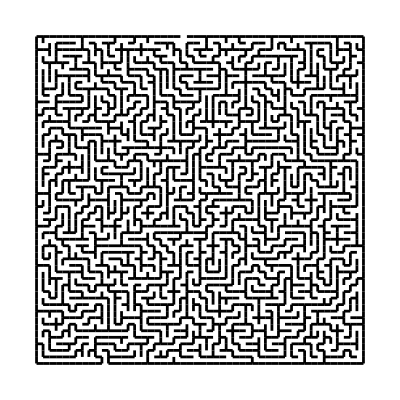

```mathematica
TimeConstrained[ResourceFunction["RandomMaze"][50],20]
```

Be sure to use delimiters between independent examples. I have added some below.

Find a solution to a random 20 by 30 maze:

```mathematica
FindRandomGridMazeSolution[{20,30}]
```

-Graphics-

Find a solution to a random 50 by 60 maze:

```mathematica
FindRandomGridMazeSolution[{50,60}]
```

-Graphics-

Find a solution to a random 60 by 70 maze:

```mathematica
FindRandomGridMazeSolution[{60,70}]
```

-Graphics-

Solve a random 70 by 80 maze:

```mathematica
FindRandomGridMazeSolution[{70,80}]
```

-Graphics-

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

mazes

graph algorithms

fun

### Categories

Cloud & Deployment
 External Interfaces & Connections
 Graphs & Networks
 Knowledge Representation & Natural Language
 Repository Tools
 Strings & Text
 User Interface Construction |  Core Language & Structure
 Financial Data & Computation
 Higher Mathematical Computation
 Machine Learning
 Scientific and Medical Data & Computation
 Symbolic & Numeric Computation
 Visualization & Graphics |  Data Manipulation & Analysis
 Geographic Data & Computation
 Images
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 System Operation & Setup
 Wolfram Physics Project |  Engineering Data & Computation
 Geometry
 Just For Fun
 Programming Utilities
 Sound & Video
 Time-Related Computation

### Related Symbols

FindShortestPath

### Related Resource Objects

RandomMaze

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

This is my first function in the fun category I think.

## Submission Notes

I am thinking of making another function FindRandomHexagonalMazeSolution and FindRandomTriangularMazeSolution based on the Resource Functions HexagonalGridGraph and TriangularGridGraph, respectively.